## Notes

>>> Note the code belows derives from internal version:  topic_model_7_alzheimers_v3_test_test_3.nb
>>>
>>> This code is not a product. It has  redundancies, error checking, unused variables,  and so forth. You may have to 
>>> enter certain things more than once.
>>> Execute all code
>>> There are notes within each major section

## Functions

>>> execute all functions before running anything else. 
>>> some functions are no longer used.
>>> execute functions in library.nb before running any code.

### Basic

```mathematica
mem[]:=Module[{mm1,mm2,share,res},
mm1=MemoryInUse[];
share=Share[];
mm2=MemoryInUse[];
res={mm1,share,mm2};
res
]
```

```mathematica
norm[p_]:=Map[N[#/Total[p]]&,p]
```

```mathematica
entropyF[v_]:=Module[{vnorm1},
vnorm=N[v/Total[v]];
lvnorm=Map[If[#==0.,0.,Log[#]]&,vnorm];
normC=-ConstantArray[N[(1/Length[v])],Length[v]].ConstantArray[N[(Log[1/Length[v]])],Length[v]];
entropy=If[normC==0.,0.,N[-vnorm.lvnorm/normC]];
entropy
]
```

```mathematica
entropyF[{1,0,0,0}]
```

0.

```mathematica
topicnum
```

topicnum

```mathematica
topTopicsF[c_]:=StringRiffle[Take[#[[1]]&/@Reverse@SortBy[MapIndexed[{#2[[1]],#1}&,c],Last],If[topicnum<3,topicnum,3]],":"]
```

```mathematica
entChoicesF[assignCur_,list_]:=Module[{end,entBeg,ent,list1},
ent={};
numTopics=Length[list];
entBeg=entropyF[list];
Do[
list1=list;
If[k≠assignCur,list1[[k]]=list1[[k]]+1,Goto[end]];
ent=Join[ent,{{assignCur,k,entBeg-entropyF[list1]}}];
Label[end];,
{k,1,numTopics}];
ent=Join[ent,{{assignCur,assignCur,0.0}}];
ent=SortBy[ent,#[[2]]&]
]
```

```mathematica
choicesF[assignCur_, list_]:=Module[{choices,list1,len},
len=Length[list];
choices=Table[{},{k,1,len}];
Do[
list1=list;
If[k≠assignCur,list1[[k]]=list1[[k]]+1,list1[[assignCur]]=list1[[assignCur]]-1];
choices[[k]]=list1,
{k,1,len}];
choices[[assignCur]]=list;
choices
]
```

```mathematica
l={1,1,1,1,1};a=2;
```

```mathematica
choicesF[a,l]
```

{{2,1,1,1,1},{1,1,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2}}

```mathematica
tt=1;lst={3,5,3,6,2};
```

```mathematica
entChoicesF[tt,lst]
```

{{1,1,0.},{1,2,0.00833376},{1,3,-0.00577138},{1,4,0.0135358},{1,5,-0.0163278}}

```mathematica
entChoicesF[tt,lst]
```

{{1,1,0.},{1,2,0.00833376},{1,3,-0.00577138},{1,4,0.0135358},{1,5,-0.0163278}}

### Graph

```mathematica
adjF1[g_,v_]:=Flatten@DeleteDuplicates@Join[{v},AdjacencyList[g,v]]
```

```mathematica
adjF2[g_,v_]:=Flatten@DeleteDuplicates@Map[Join[{#},AdjacencyList[g,#]]&,DeleteDuplicates@Join[{v},AdjacencyList[g,v]]]
```

```mathematica
adjF3[g_,v_]:=Flatten@DeleteDuplicates@Map[Join[{#},AdjacencyList[g,#]]&,v]
```

>>> Start

## Data Loading

>>> Edit the directory.
>>> Edit the filenames. You may have to enter the same name more than once.
>>> tk1 file format is tab delimited: id, curly-bracketed list of microbial objects.
>>> tk2 file format is tab delimited: id, sample id, curly-bracketed list of microbial objects.

```mathematica
SetDirectory["/Users/jeffreylapides/Documents/Mathematica_new/alzheimers"];
```

```mathematica
datatest=ToExpression[Import["microbiome_alzheimer's_input_11_s1.tsv"]];
Length@%
```

123

```mathematica
datatest[[1]]
```

{1,{Propionibacterium_acnes-14,Veillonella-9,Klebsiella-10,Streptococcus-12}}

```mathematica
datacheck=ToExpression[Import["microbiome_alzheimer's_input_11_s1.tsv"]];
Length@%
tk1check=ToExpression[Import["microbiome_alzheimer's_input_11_s1.tsv","TSV"]];
Length@%
tk2check={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@Import["microbiome_alzheimer's_input_11a_s1.tsv","TSV"];
Length@%
```

123

123

123

```mathematica
tk1=ToExpression[Import["microbiome_alzheimer's_input_11_s1.tsv","TSV"]];
Length@%
```

123

```mathematica
tk2={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@Import["microbiome_alzheimer's_input_11a_s1.tsv","TSV"];
Length@%
```

123

```mathematica
tk2[[1]]
```

{1,2016P1_lbc10,{Propionibacterium_acnes-14,Veillonella-9,Klebsiella-10,Streptococcus-12}}

```mathematica
inputFilename="microbiome_alzheimer's_input_11_s1.tsv";
```

```mathematica
Do[tkixTname[tk2[[i,1]]]=tk2[[i,2]],{i,1,Length[tk2]}]
```

>>> load metadata (note: this has been corrected for earlier labeling errors)
>>> note for JL: see topic_model_7_alzheimers_v4.nb for source

```mathematica
md1=Import["md1UAMS.csv", "CSV"];
```

## Classification Model

### Parameters and Setup

>>> move into main code?

>>> Notes:

```mathematica
(*-----------Future for Automated reurn comparisons-----------*)
(*reTest=1; *)
(*dt1OutputOld={}; *)
(*vocabTopic5IntOld={}; *)
(*****************************)
```

>>> The following code comprises input parameters for the classifier code, output file naming, read.me file >>> info. Export file names are dynamically created for results exports. Parameters used for file naming are >>> noted.  Look at prefix to see how they are used. Other variables are described in the comments within the >>> code.
>>> Vocab and related variables refer to the microbial objects. Name comes from sets of words from topic 
>>> modeling.

```mathematica
runVal="15.0";
rerun="XX";
tm="5"; (*code version*)
frq=20;(*printing*)
name="Alzheimers";
nameExt="_AK_";
(*--------------ENTER NOTE FOR README FILE---------------------*)
(*Most parameters below are recorded in readme file automatically*)
note="alzheimer's, AK only, negative controls removed, edited to remove samples with no metadata, negative controls removed, edited to remove samples with no metadata,  Genus and species hybrid (Propionibacterium, Acinetobacter, Comamonas, Option 8a, retains name specificity, mu/nu=0.98, burnin:99, mu/nu kickin at 149,  very nice graph definition";

(*--------------CLASSIFIER PARAMETERS---------------------*)
topicnum=5;
numTopics=topicnum;(*some code uses numTopics. This sets to topicnum*)
reset =0; (*NEW*)
wordColnum=2;(*position of microbial objects in tk1, datacheck, datatest, etc.*)
datacol=3; (*NEW - not used*)
wordCutoff=1(*wordCutoff is a filter on vocab counts. It is executed in vocab setup. Only objects with total counts that exceed wordcutoff go into the vocab used for the classification*)
subjLen=1;(*probably should be called sample length, used to filter for samples that have at least subjlen number of microbial objects*)
(*Classifier Formula from Classifier below*)
(*distUpd=N[delta*docTopic3Cur2^gammad*vocabDist2^gammav/sumNorm+alpha*vocabDist2/sumNorm+beta*docTopic3Cur2/sumNorm+alpha*beta/sumNorm];*)
(*docTopic3Cur2: sample class distribution, SD from paper*)
(*vocabDist2: object distribution, OD from paper*)
(*sumNorm is normalization factor computed below in Classifier*)
(*CLASSIFIER PARAMETERS FROM FORMULA ABOVE*)
alpha=0.3;
beta=0.25;
delta=1.0;
gammad=1.0;
gammav=1.0;
mu=0.96; (*sample trimming parameter, cited as 1-mu in paper*)
nu=0.96; (*object trimming parameter, cited as 1-nu in paper*)
cutoffComp=0.75; (*not currently used*)
finalEntropies=""; (*Initialization for text variable describing final average entropies for both samples and objects*)
topics=Range[1,topicnum];
dmax=Length[datatest];
k=0;
(*--------------MORE CLASSIFIER PARAMETERS----------------*)
cumNum=99; (*burn-in iterations*)
nSumAvg=149; (*iteration where classsifier mixing begins*)
docSum=123;(*number of samples*)
cumFreq=5;(*thinning parameter in iterations*)
dmin=1; nmax=1000; (*iteration beginning and end*)
nVoc=1;(*used dto adjust low count object distribution during burn-in*)
nSubj=1;(*used to adjust low count sample distribution during burn-in*)
nDie=1;  (*used to adjust classifier for low count objects during burn-in *)
(*--------------COMPUTE Export Filename Prefix, Readme----------------*)
topicsVal=ToString[topicnum]<>"_topics_";
alphaVal="a_"<>StringReplace[ToString[alpha],"."->"P"]<>"_";
betaVal="b_"<>StringReplace[ToString[beta],"."->"P"]<>"_";
cutoffVal="cut_"<>ToString[wordCutoff]<>"_";
subdir=name<>"_results";
prefix=name<>nameExt<>topicsVal<>alphaVal<>betaVal<>cutoffVal<>runVal<>"rr"<>ToString[rerun];
readme=name<>nameExt<>"\n"<>"TopicNum: "<>ToString[topicnum]<>"\n"<>
"Run #: "<>ToString[runVal]<>"rr"<>ToString[rerun]"\n"<>
"Input filename: "<>inputFilename<>"\n"<>
"Word Column Num: "<>ToString[wordColnum]<>"\n"<>
"Word Cutoff: "<>ToString[wordCutoff]<>"\n"<>
"Subject Length Cutoff: "<>ToString[subjLen]<>"\n"<>
"alpha: "<>ToString[alpha]<>"\n"<>
"beta: "<>ToString[beta]<>"\n"<>
"gammad: "<>ToString[gammad]<>"\n"<>
"gammav: "<>ToString[gammav]<>"\n"<>
"delta: "<>ToString[delta]<>"\n"<>
"option: "<>ToString[option]<>"\n"<>
"TM: "<>tm<>"\n"<>
"# of entities: "<>ToString[Length@datatest1]<>"\n"<>
"Cumulative starting point: "<>ToString[cumNum]<>", Cumulative Frequency: "<>ToString[cumFreq]<>"\n"<>
finalEntropies<>
"# of Iterations: "<>ToString[nmax]<>"\n"<>note;
```

1

### Object Merging

>>> code that merges low count objects into single objects
>>> code that reduces the resolution of abundance bins to two, hi and lo

#### Setup

```mathematica
datacheck1=Select[Map[#[[wordColnum]]&,datacheck],Length[#]>=subjLen&];
vocabcheckCnt=Select[SortBy[Tally[Flatten[datacheck1]],First],#[[2]]>wordCutoff&&MemberQ[{"plus","minus"},Last[StringSplit[#[[1]],"-"]]]==False&];
vocabcheckCntLst=#[[1]]&/@vocabcheckCnt;
```

```mathematica
Length@datacheck1
```

123

```mathematica
tk1check={#[[1]],Reverse@(SortBy[#[[2]],ToExpression[Last[StringSplit[#,"-"]]]&])}&/@tk1check;
Length@%
allTable10=Table[{md1[[i]],tk1check[[i]]},{i,1,Length@tk1check}];
Length@%
allTable14=Map[{{#[[1,1]],#[[1,2]],#[[1,3]],Switch[StringTake[#[[1,6]],2],"AD","AK","NW","NW"]},{#[[2,1]],#[[2,2]]}}&,allTable10];
Length@%
```

123

123

123

```mathematica
diseaseStat={N[(#[[1,1,2]]-1)/(#[[1,1,2]]-1+#[[1,2,2]]-1),3],#[[2]],{{"AD",#[[1,1,2]]-1},{"C",#[[1,2,2]]-1}},{"TOT",(#[[1,1,2]]-1+#[[1,2,2]]-1)}}&/@(Table[{(Tally[Join[{"AD","C"},(#[[1,2]]&/@Select[allTable14,MemberQ[#[[2,2]],vocabcheckCntLst[[i]]]&])]]),vocabcheckCntLst[[i]]},{i,1,Length@vocabcheckCntLst}]);
Length@%
```

218

```mathematica
microbesLst=Sort@DeleteDuplicates[ss1F[#[[2]]]&/@diseaseStat]
Length@%
```

{Achromobacter,Acidovorax,Acinetobacter_baumannii,Acinetobacter_guillouiae,Acinetobacter_junii,Acinetobacter_tjernbergiae,Actinomyces,Anaerococcus,Aquabacterium,Bacillus,Bacteroides,Blastomonas,Blautia,Bosea,Bradyrhizobium,Brevibacterium,Brevundimonas,Caulobacter,Christensenella,Chryseobacterium,Cloacibacterium,Clostridium,Comamonas_denitrificans,Comamonas_jiangduensis,Comamonas_nitrativorans,Comamonas_terrae,Comamonas_testosteroni,Corynebacterium,Cupriavidus,Cutibacterium,Cylindrospermum,Delftia,Devosia,Dietzia,Enterococcus,Finegoldia,Flavobacterium,Gemella,Herbaspirillum,Hyphomicrobium,Janibacter,Janthinobacterium,Klebsiella,Kocuria,Lachnoclostridium,Lactobacillus,Meiothermus,Methylobacterium,Microbacterium,Micrococcus,Microlunatus,Moraxella,Nitrosospira,Noviherbaspirillum,Novosphingobium,Oscillibacter,Ottowia,Pedobacter,Peptoniphilus,Prevotella,Propionibacterium_acnes,Pseudomonas,Ralstonia,Reyranella,Rhodococcus,Rothia,Ruminiclostridium,Schlegelella,Sediminibacterium,Snodgrassella,Sphingobium,Sphingomonas,Staphylococcus,Stenotrophomonas,Streptococcus,Tyzzerella,Variovorax,Veillonella,Vulcaniibacterium,Zoogloea}

80

```mathematica
microbesCnt=Table[{microbesLst[[i]],Total[{#[[3,1,2]],#[[3,2,2]],#[[4,2]]}&/@Select[diseaseStat,ss1F[#[[2]]]==microbesLst[[i]]&&ss2F[#[[2]]]≥1&]]},{i,1,Length@microbesLst}]
Length@%
```

{{Achromobacter,{5,8,13}},{Acidovorax,{25,23,48}},{Acinetobacter_baumannii,{1,6,7}},{Acinetobacter_guillouiae,{1,1,2}},{Acinetobacter_junii,{27,35,62}},{Acinetobacter_tjernbergiae,{25,31,56}},{Actinomyces,{1,1,2}},{Anaerococcus,{6,8,14}},{Aquabacterium,{2,4,6}},{Bacillus,{9,2,11}},{Bacteroides,{1,3,4}},{Blastomonas,{3,3,6}},{Blautia,{0,2,2}},{Bosea,{6,1,7}},{Bradyrhizobium,{11,8,19}},{Brevibacterium,{2,1,3}},{Brevundimonas,{1,2,3}},{Caulobacter,{2,0,2}},{Christensenella,{2,0,2}},{Chryseobacterium,{5,4,9}},{Cloacibacterium,{17,24,41}},{Clostridium,{0,2,2}},{Comamonas_denitrificans,{4,0,4}},{Comamonas_jiangduensis,{1,21,22}},{Comamonas_nitrativorans,{2,0,2}},{Comamonas_terrae,{0,2,2}},{Comamonas_testosteroni,{12,8,20}},{Corynebacterium,{15,10,25}},{Cupriavidus,{0,2,2}},{Cutibacterium,{1,3,4}},{Cylindrospermum,{2,0,2}},{Delftia,{11,12,23}},{Devosia,{1,1,2}},{Dietzia,{2,0,2}},{Enterococcus,{4,3,7}},{Finegoldia,{0,2,2}},{Flavobacterium,{0,4,4}},{Gemella,{2,0,2}},{Herbaspirillum,{2,2,4}},{Hyphomicrobium,{2,0,2}},{Janibacter,{2,0,2}},{Janthinobacterium,{2,0,2}},{Klebsiella,{1,3,4}},{Kocuria,{8,5,13}},{Lachnoclostridium,{2,3,5}},{Lactobacillus,{4,6,10}},{Meiothermus,{6,2,8}},{Methylobacterium,{12,0,12}},{Microbacterium,{1,4,5}},{Micrococcus,{1,1,2}},{Microlunatus,{1,1,2}},{Moraxella,{16,21,37}},{Nitrosospira,{13,9,22}},{Noviherbaspirillum,{7,1,8}},{Novosphingobium,{12,6,18}},{Oscillibacter,{2,0,2}},{Ottowia,{2,2,4}},{Pedobacter,{1,1,2}},{Peptoniphilus,{2,0,2}},{Prevotella,{2,0,2}},{Propionibacterium_acnes,{56,45,101}},{Pseudomonas,{10,23,33}},{Ralstonia,{3,2,5}},{Reyranella,{1,1,2}},{Rhodococcus,{3,2,5}},{Rothia,{1,1,2}},{Ruminiclostridium,{2,0,2}},{Schlegelella,{2,0,2}},{Sediminibacterium,{18,15,33}},{Snodgrassella,{1,1,2}},{Sphingobium,{7,1,8}},{Sphingomonas,{5,6,11}},{Staphylococcus,{5,2,7}},{Stenotrophomonas,{7,8,15}},{Streptococcus,{9,19,28}},{Tyzzerella,{1,1,2}},{Variovorax,{4,0,4}},{Veillonella,{1,3,4}},{Vulcaniibacterium,{2,1,3}},{Zoogloea,{8,5,13}}}

80

>>> Hybrid Genus/Species level

```mathematica
propionibacteriumJ=DeleteDuplicates[StringSplit[#[[2]],"-"][[1]]&/@Select[diseaseStat,StringSplit[#[[2]],"_"][[1]]=="Propionibacterium"&]]
```

{Propionibacterium_acnes}

```mathematica
acinetobacterJ=DeleteDuplicates[StringSplit[#[[2]],"-"][[1]]&/@Select[diseaseStat,StringSplit[#[[2]],"_"][[1]]=="Acinetobacter"&]]
```

{Acinetobacter_baumannii,Acinetobacter_guillouiae,Acinetobacter_junii,Acinetobacter_tjernbergiae}

```mathematica
comamonasJ=DeleteDuplicates[StringSplit[#[[2]],"-"][[1]]&/@Select[diseaseStat,StringSplit[#[[2]],"_"][[1]]=="Comamonas"&]]
```

{Comamonas_denitrificans,Comamonas_jiangduensis,Comamonas_nitrativorans,Comamonas_terrae,Comamonas_testosteroni}

```mathematica
collapsers=DeleteDuplicates[ss1F[#[[2]]]&/@Select[diseaseStat,ss2F[#[[2]]]>=12&&StringSplit[#[[2]],"_"][[1]]≠"Propionibacterium"&&StringSplit[#[[2]],"_"][[1]]≠"Acinetobacter"&&StringSplit[#[[2]],"_"][[1]]≠"Comamonas"&&#[[4,2]]≥3&]]
```

{Achromobacter,Acidovorax,Bacillus,Bradyrhizobium,Brevibacterium,Brevundimonas,Cloacibacterium,Corynebacterium,Delftia,Kocuria,Meiothermus,Methylobacterium,Moraxella,Nitrosospira,Noviherbaspirillum,Novosphingobium,Pseudomonas,Sediminibacterium,Stenotrophomonas,Streptococcus}

```mathematica
collapser1=Join[collapsers,propionibacteriumJ,acinetobacterJ, comamonasJ]
```

{Achromobacter,Acidovorax,Bacillus,Bradyrhizobium,Brevibacterium,Brevundimonas,Cloacibacterium,Corynebacterium,Delftia,Kocuria,Meiothermus,Methylobacterium,Moraxella,Nitrosospira,Noviherbaspirillum,Novosphingobium,Pseudomonas,Sediminibacterium,Stenotrophomonas,Streptococcus,Propionibacterium_acnes,Acinetobacter_baumannii,Acinetobacter_guillouiae,Acinetobacter_junii,Acinetobacter_tjernbergiae,Comamonas_denitrificans,Comamonas_jiangduensis,Comamonas_nitrativorans,Comamonas_terrae,Comamonas_testosteroni}

```mathematica
microbesCntGTECut=Select[microbesCnt,#[[2,3]]≥5&&(MemberQ[propionibacteriumJ,#[[1]]]==False&&MemberQ[acinetobacterJ,#[[1]]]==False)&];
microbesCntGTECutLst=complement[#[[1]]&/@microbesCntGTECut,collapsers]
Length@%
```

{Anaerococcus,Aquabacterium,Blastomonas,Bosea,Chryseobacterium,Comamonas_jiangduensis,Comamonas_testosteroni,Enterococcus,Lachnoclostridium,Lactobacillus,Microbacterium,Ralstonia,Rhodococcus,Sphingobium,Sphingomonas,Staphylococcus,Zoogloea}

17

>>> Histogram of number of objects per sample, for informational purposes

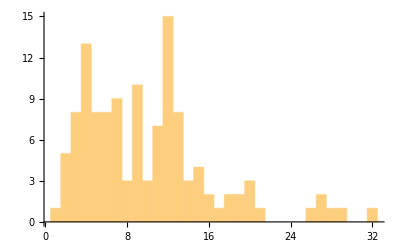

```mathematica
Histogram[Length[#[[2]]]&/@datatest,{1}]
```

#### Object Merging Computation

>>> Option 8a for hybrid discretization, uses both species and genus level objects
>>> Many options were tried. This gave the best results.

```mathematica
option="8a";
tk2={#[[1]],#[[2]],If[MemberQ[collapser1,ss1F[#]],If[(StringSplit[ss1F[#],"_"][[1]]=="Propionibacterium"||StringSplit[ss1F[#],"_"][[1]]=="Acinetobacter"),If[ss2F[#]≥12,#,ss1F[#]<>"-lo"],If[ss2F[#]≥12,ss1F[#]<>"-hi",ss1F[#]<>"-lo"]],If[ss2F[#]==14,#,If[ss2F[#]≥12&&MemberQ[microbesCntGTECutLst,ss1F[#]],ss1F[#]<>"-hi",If[ss2F[#]<=11&&MemberQ[microbesCntGTECutLst,ss1F[#]],Nothing, Nothing]]]]&/@#[[3]]}&/@tk2;
datacheck2=Select[#[[3]]&/@tk2,Length[#]>=subjLen&];
Length@%
vocabCol=Select[SortBy[Tally[Flatten[datacheck2]],First],#[[2]]>wordCutoff&&MemberQ[{"plus","minus"},Last[StringSplit[#[[1]],"-"]]]==False&];
Length@%
objectsLoCntLst=#[[1]]&/@Select[vocabCol,#[[2]]≤4&& (ss1F[#[[1]]]=="Propionibacterium"||ss1F[#[[1]]]=="Acinetobacter")==False&];
Length@%
tk2={#[[1]],#[[2]],If[MemberQ[objectsLoCntLst,#],"LoCnt-"<>ToString[ss2F[#]],#]&/@#[[3]]}&/@tk2;
tk1={#[[1]], #[[3]]}&/@tk2;
tk1graph=tk1;
datatest=tk1;
```

123

69

20

```mathematica
vocabCol//TableForm
Length@vocabCol
```

Achromobacter-hi | 7
Achromobacter-lo | 8
Acidovorax-hi | 22
Acidovorax-lo | 26
Acinetobacter_baumannii-lo | 9
Acinetobacter_guillouiae-lo | 3
Acinetobacter_junii-12 | 8
Acinetobacter_junii-13 | 22
Acinetobacter_junii-14 | 17
Acinetobacter_junii-lo | 15
Acinetobacter_tjernbergiae-12 | 9
Acinetobacter_tjernbergiae-13 | 17
Acinetobacter_tjernbergiae-14 | 9
Acinetobacter_tjernbergiae-lo | 21
Anaerococcus-hi | 3
Bacillus-hi | 6
Bacillus-lo | 8
Bosea-hi | 2
Bradyrhizobium-hi | 6
Bradyrhizobium-lo | 15
Brevibacterium-hi | 3
Brevundimonas-hi | 4
Brevundimonas-lo | 2
Caulobacter-14 | 2
Chryseobacterium-hi | 2
Cloacibacterium-hi | 20
Cloacibacterium-lo | 23
Comamonas_denitrificans-lo | 8
Comamonas_jiangduensis-hi | 14
Comamonas_jiangduensis-lo | 9
Comamonas_nitrativorans-lo | 3
Comamonas_terrae-lo | 3
Comamonas_testosteroni-hi | 3
Comamonas_testosteroni-lo | 19
Corynebacterium-hi | 4
Corynebacterium-lo | 22
Delftia-hi | 9
Delftia-lo | 15
Enterococcus-hi | 2
Janthinobacterium-14 | 2
Kocuria-hi | 8
Kocuria-lo | 8
Meiothermus-hi | 6
Meiothermus-lo | 4
Methylobacterium-hi | 8
Methylobacterium-lo | 5
Moraxella-hi | 12
Moraxella-lo | 25
Nitrosospira-hi | 14
Nitrosospira-lo | 10
Noviherbaspirillum-hi | 6
Noviherbaspirillum-lo | 2
Novosphingobium-hi | 4
Novosphingobium-lo | 16
Propionibacterium_acnes-12 | 13
Propionibacterium_acnes-13 | 23
Propionibacterium_acnes-14 | 43
Propionibacterium_acnes-lo | 22
Pseudomonas-hi | 13
Pseudomonas-lo | 22
Sediminibacterium-hi | 16
Sediminibacterium-lo | 17
Sphingomonas-14 | 2
Stenotrophomonas-hi | 6
Stenotrophomonas-lo | 11
Streptococcus-hi | 8
Streptococcus-lo | 23
Variovorax-14 | 2
Zoogloea-hi | 2

69

```mathematica
objectsLoCntLst//TableForm
Length@%
```

Acinetobacter_guillouiae-lo
Anaerococcus-hi
Bosea-hi
Brevibacterium-hi
Brevundimonas-hi
Brevundimonas-lo
Caulobacter-14
Chryseobacterium-hi
Comamonas_nitrativorans-lo
Comamonas_terrae-lo
Comamonas_testosteroni-hi
Corynebacterium-hi
Enterococcus-hi
Janthinobacterium-14
Meiothermus-lo
Noviherbaspirillum-lo
Novosphingobium-hi
Sphingomonas-14
Variovorax-14
Zoogloea-hi

20

### Microbial Object Vocabulary Setup

```mathematica
vocabzeroCnt=0;doczeroCnt=0;
datacheck1=Map[#[[wordColnum]]&,datacheck];
vocabcheckCnt=SortBy[Tally[Flatten[datacheck1]],First];
docCaseEntDiffAcc={};vocabCaseEntDiffAcc={};
datatest1=Map[#[[wordColnum]]&,datatest];(*Grab word list from raw data*)
vocabCnt=SortBy[Tally[Flatten[datatest1]],First];
vocabFlt=#[[1]]&/@Select[vocabCnt,#[[2]]>wordCutoff&&MemberQ[{"plus","minus"},Last[StringSplit[#[[1]],"-"]]]==False&];
datatest1=Map[Intersection[#,vocabFlt]&,datatest1];(*grab words in count-filtered vocabulary*)
Print["S1: ", Length@datatest1];
datatest1=Map[Select[#,MemberQ[vocabFlt,#]&]&,datatest1];(*The line above should not change the above, don't know why it is here, is probably better than above line because dups could cause Intersection to fail*)
(*datatest1=Join[#,Table["ran"<>ToString[RandomInteger[4]+1],{k,1,1}]]&/@datatest1;*)
Print["S2: ", Length@datatest1];
datatest1N=number[datatest1];
Print["S3N: ", Length@datatest1N];
datatest1=Select[datatest1,#≠{}&&Length[#]>=subjLen&];
vocabCnt1=SortBy[Tally[Flatten[datatest1]],First];
dataIX=#[[1]]&/@Select[datatest1N,#[[2]]≠{}&&Length[#[[2]]]>=subjLen&];
Print["S3: ", Length@datatest1];
Print["S4IX: ", Length@dataIX];
dmax=Length[datatest1]; (*Recompute document count in case previous step filtered some docs*)
vocab=Sort@DeleteDuplicates[Flatten[datatest1]];(*redefine vocab from filtered vocabulary*)
vmax=Length@vocab;
Do[vocabIX[vocab[[i]]]=i,{i,1,Length@vocab}](*index vocab, e.g. vocabIX["biomarker"]*)
assigns=Map[{#,vocabIX[#],RandomInteger[{1,topicnum}]}&,datatest1,{2}];(*initial random assignment by doc, {word, word index, topic}*)
wmax=Length[#]&/@assigns;
vocabTopic1=Map[SortBy[Tally[#],First]&,Map[#[[3]]&,GatherBy[SortBy[Flatten[assigns,1],First],#[[1]]&],{2}]];(*for each word in vocab, counts by topic, sorted by topic*)
vocabTopic2=SparseArray[Flatten[MapIndexed[{#2[[1]],#1[[1]]}->#1[[2]]&,vocabTopic1,{2}],1]];
vocabTopic3=Normal[vocabTopic2];(*first element of vocab1 list, counts, seems like I coud get directly from vocabTopic1 and bypass vocabTopic2 - CIRCLE BACK,*)
vocabTopicDist=Map[norm[#]&,vocabTopic3];(*normalized topic distribution for each vocab word*)
docTopic1=MapIndexed[{#2[[1]],#1[[1]]}->#1[[2]]&,Map[SortBy[Tally[#],First]&,Map[ #[[3]]&,assigns,{2}]],{2}];
docTopic2=SparseArray[Flatten[docTopic1,1]];
docTopic3=Normal[docTopic2];(*counts by topic for each doc*)
docTopicDist=Map[norm[#]&,docTopic3]; (*normalized topic distribution for each doc*)
docTopic3EntBeg=Total[Map[entropyF[#]&,docTopic3]]; (*total entropy of documents*)
sumV=Total[vocabTopic3];(*total counts for each topic*)
vocabTopic3EntAcc=Total[Map[entropyF[#]&,vocabTopic3]];(*total entropy of vocabulary*)
vocabTopic3EntAccBeg=vocabTopic3EntAcc(*copy beginning vocabulary entropy to new variable to preserve starting value*)
vocabTopic3EntAccBegperTok=vocabTopic3EntAccBeg/vmax
docTopic3EntBegperdoc=docTopic3EntBeg/dmax
order1=Range[1,Length[assigns]];
order2=Range[1,Length[assigns]];
order1Reo=Range[1,Length[assigns]];
docTopic3Tot=Table[Total[docTopic3[[i]]],{i,1,Length@docTopic3}]
```

S1: 123

S2: 123

S3N: 123

S3: 122

S4IX: 122

45.0151

0.865675

0.680935

{2,2,4,2,4,7,5,4,1,3,2,4,2,2,6,2,2,2,3,4,6,3,6,8,2,7,6,7,3,5,6,9,9,4,10,6,7,4,10,6,8,7,6,2,11,5,6,11,9,9,9,8,4,9,8,5,5,4,9,6,3,3,11,15,11,12,9,13,3,7,11,7,6,7,6,6,6,5,10,8,9,11,11,9,4,10,12,8,5,8,5,8,3,8,8,7,6,8,7,10,8,9,13,3,6,4,6,6,2,2,5,2,3,5,3,3,8,2,2,3,4,5}

```mathematica
ReverseSortBy[vocabCnt1,#[[2]]&]//TableForm
Length@vocabCnt1
```

Propionibacterium_acnes-14 | 43
LoCnt-hi | 26
Acidovorax-lo | 26
Moraxella-lo | 25
Streptococcus-lo | 23
Propionibacterium_acnes-13 | 23
Cloacibacterium-lo | 23
Pseudomonas-lo | 22
Propionibacterium_acnes-lo | 22
Corynebacterium-lo | 22
Acinetobacter_junii-13 | 22
Acidovorax-hi | 22
Acinetobacter_tjernbergiae-lo | 21
Cloacibacterium-hi | 20
Comamonas_testosteroni-lo | 19
Sediminibacterium-lo | 17
Acinetobacter_tjernbergiae-13 | 17
Acinetobacter_junii-14 | 17
Sediminibacterium-hi | 16
Novosphingobium-lo | 16
LoCnt-lo | 16
Delftia-lo | 15
Bradyrhizobium-lo | 15
Acinetobacter_junii-lo | 15
Nitrosospira-hi | 14
Comamonas_jiangduensis-hi | 14
Pseudomonas-hi | 13
Propionibacterium_acnes-12 | 13
Moraxella-hi | 12
Stenotrophomonas-lo | 11
Nitrosospira-lo | 10
Delftia-hi | 9
Comamonas_jiangduensis-lo | 9
Acinetobacter_tjernbergiae-14 | 9
Acinetobacter_tjernbergiae-12 | 9
Acinetobacter_baumannii-lo | 9
Streptococcus-hi | 8
Methylobacterium-hi | 8
Kocuria-lo | 8
Kocuria-hi | 8
Comamonas_denitrificans-lo | 8
Bacillus-lo | 8
Acinetobacter_junii-12 | 8
Achromobacter-lo | 8
LoCnt-14 | 7
Achromobacter-hi | 7
Stenotrophomonas-hi | 6
Noviherbaspirillum-hi | 6
Meiothermus-hi | 6
Bradyrhizobium-hi | 6
Bacillus-hi | 6
Methylobacterium-lo | 5

52

### Classification Code

>>> remove comments

Wed 30 Mar 2022 13:40:30GMT-4[]

Beginning vocab Entropy: 0.865675, Beginning doc Entropy: 0.680935

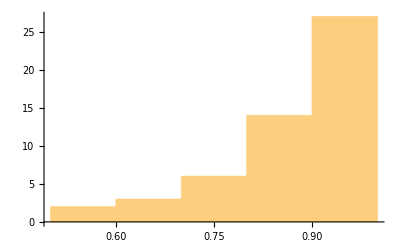

n= 20, Vocab Entropy:0., Doc Entropy:0.397762

-Graphics-

-Graphics-

n= 40, Vocab Entropy:0., Doc Entropy:0.374851

-Graphics-

-Graphics-

n= 60, Vocab Entropy:0., Doc Entropy:0.409254

-Graphics-

-Graphics-

n= 80, Vocab Entropy:0., Doc Entropy:0.373667

-Graphics-

-Graphics-

n= 100, Vocab Entropy:0.265034, Doc Entropy:0.389633

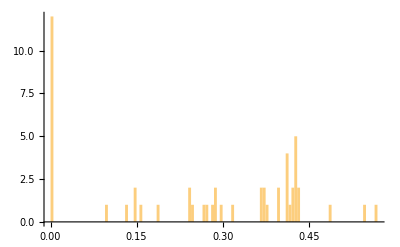

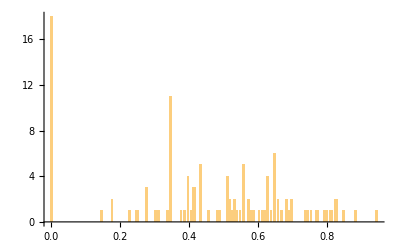

n= 120, Vocab Entropy:0.331527, Doc Entropy:0.360181

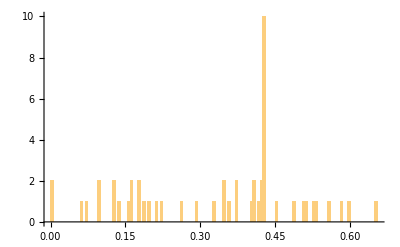

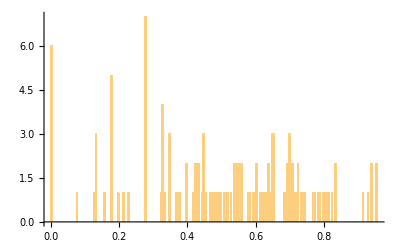

n= 140, Vocab Entropy:0.371604, Doc Entropy:0.361248

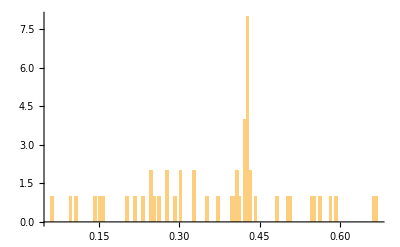

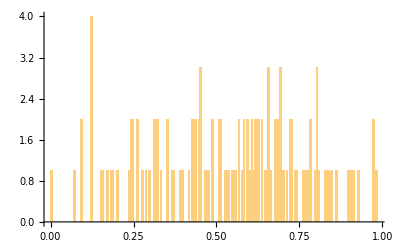

n= 160, Vocab Entropy:0.374985, Doc Entropy:0.386384

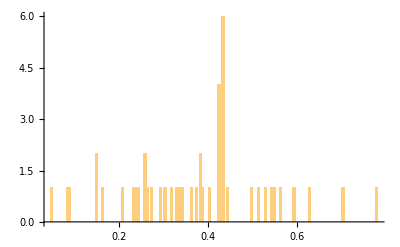

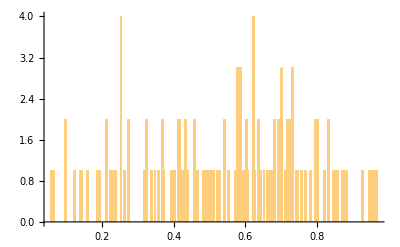

n= 180, Vocab Entropy:0.379174, Doc Entropy:0.382892

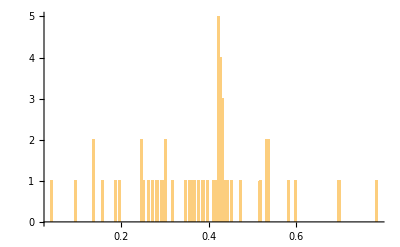

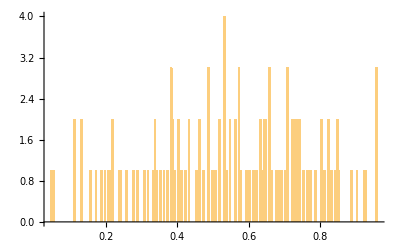

n= 200, Vocab Entropy:0.379086, Doc Entropy:0.37636

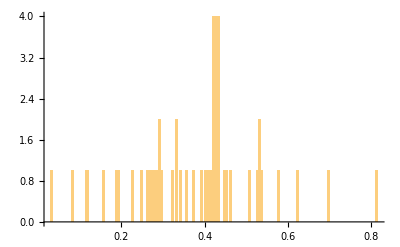

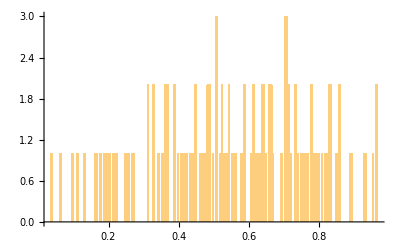

n= 220, Vocab Entropy:0.37986, Doc Entropy:0.359617

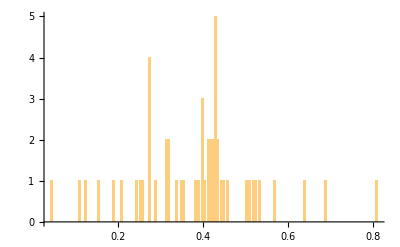

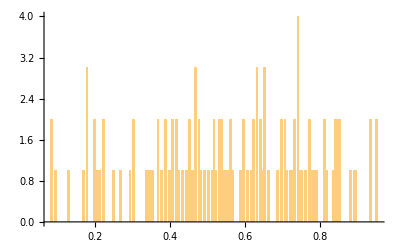

n= 240, Vocab Entropy:0.382365, Doc Entropy:0.364362

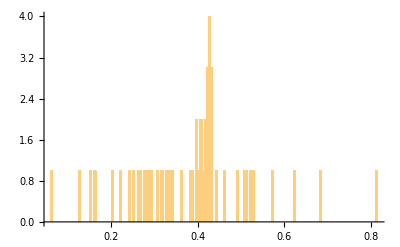

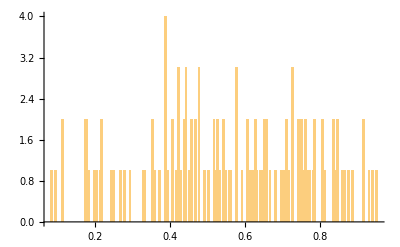

n= 260, Vocab Entropy:0.383326, Doc Entropy:0.368723

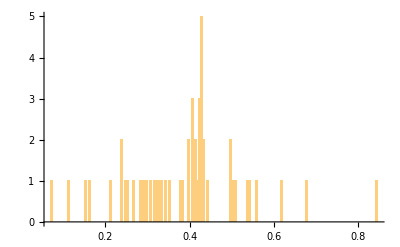

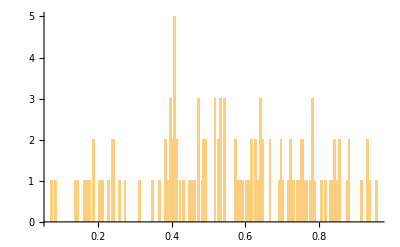

n= 280, Vocab Entropy:0.386523, Doc Entropy:0.383411

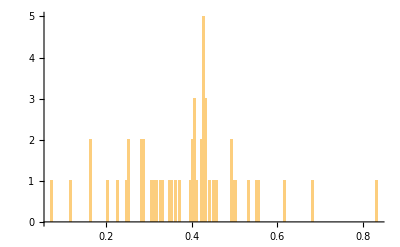

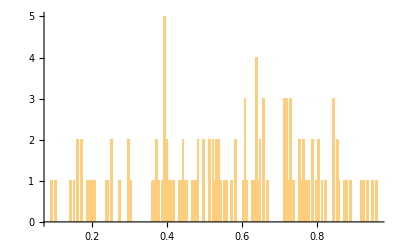

n= 300, Vocab Entropy:0.387621, Doc Entropy:0.390526

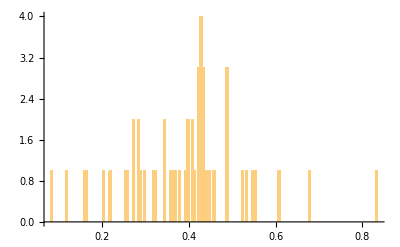

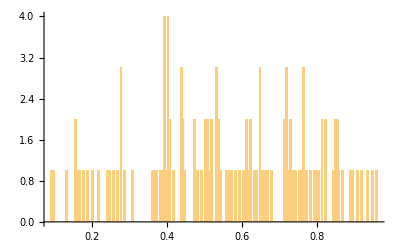

n= 320, Vocab Entropy:0.386741, Doc Entropy:0.40588

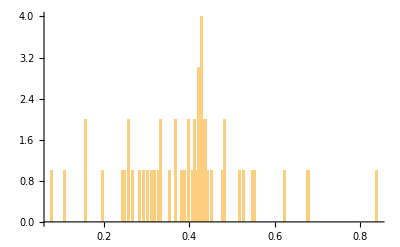

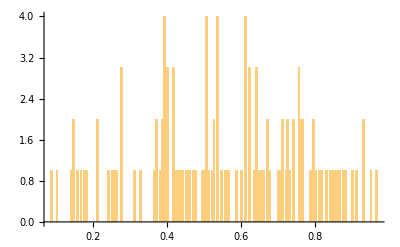

n= 340, Vocab Entropy:0.386475, Doc Entropy:0.392839

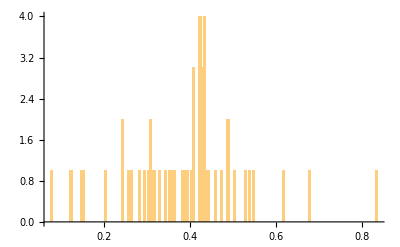

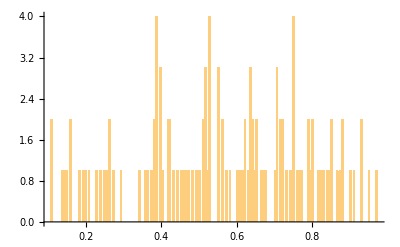

n= 360, Vocab Entropy:0.385915, Doc Entropy:0.410147

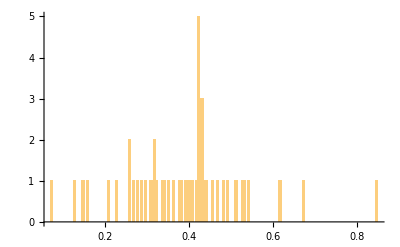

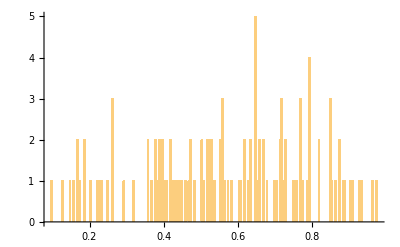

n= 380, Vocab Entropy:0.385464, Doc Entropy:0.399065

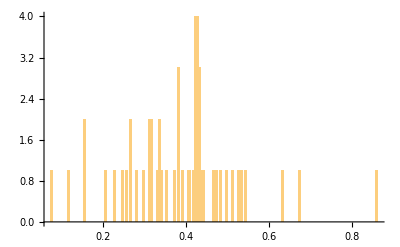

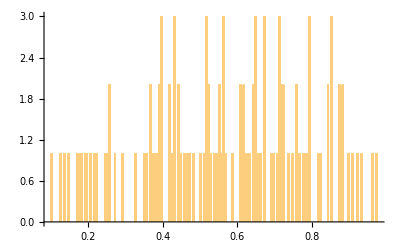

n= 400, Vocab Entropy:0.385797, Doc Entropy:0.397221

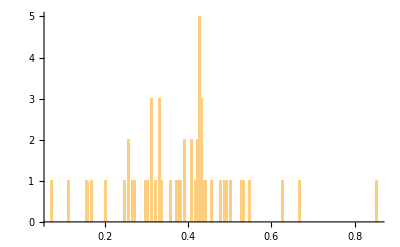

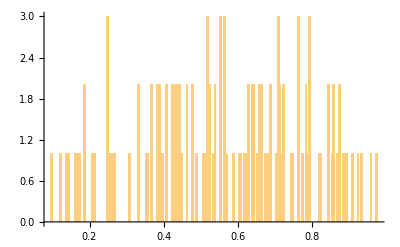

n= 420, Vocab Entropy:0.385629, Doc Entropy:0.387458

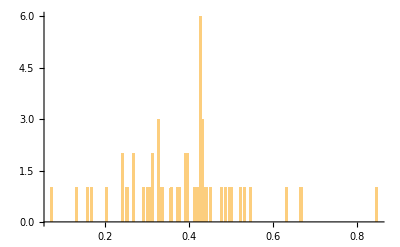

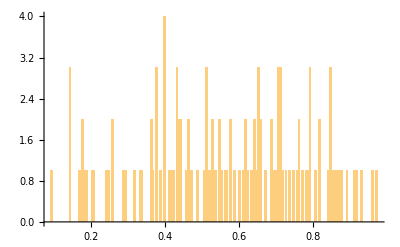

n= 440, Vocab Entropy:0.387232, Doc Entropy:0.354176

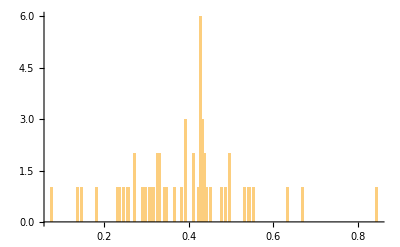

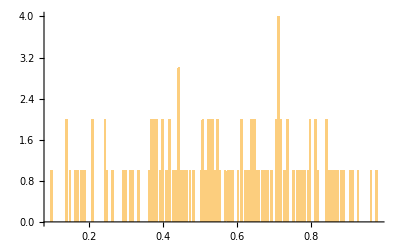

n= 460, Vocab Entropy:0.388137, Doc Entropy:0.383294

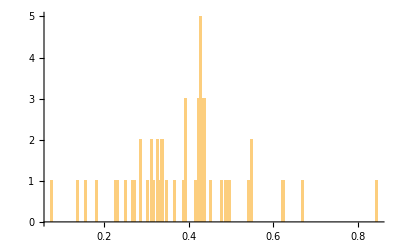

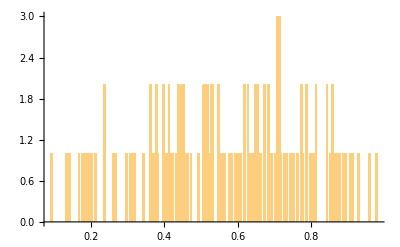

n= 480, Vocab Entropy:0.389256, Doc Entropy:0.366562

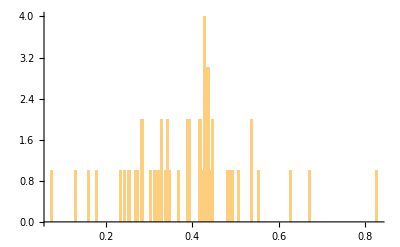

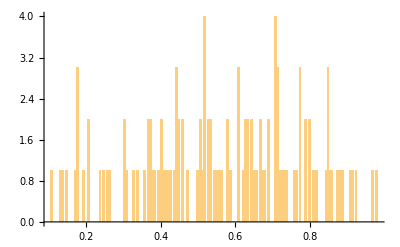

n= 500, Vocab Entropy:0.389251, Doc Entropy:0.371

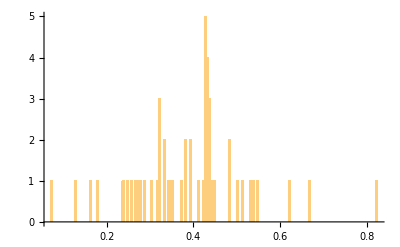

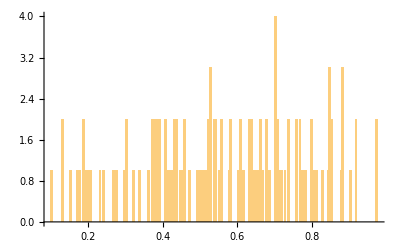

n= 520, Vocab Entropy:0.389368, Doc Entropy:0.369957

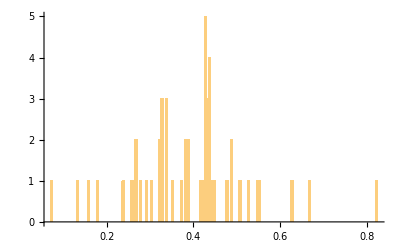

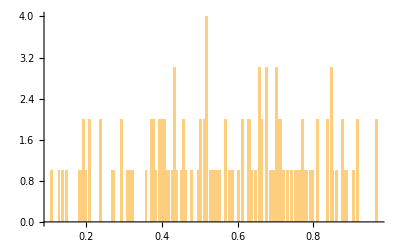

n= 540, Vocab Entropy:0.389435, Doc Entropy:0.379643

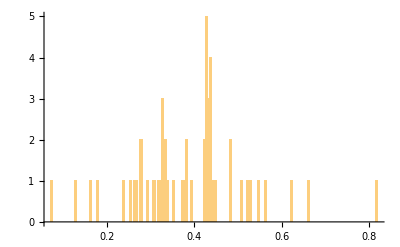

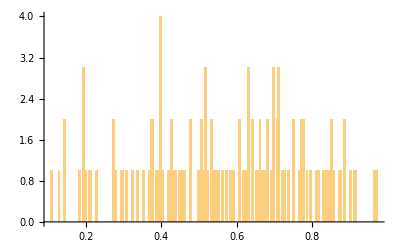

n= 560, Vocab Entropy:0.389161, Doc Entropy:0.354288

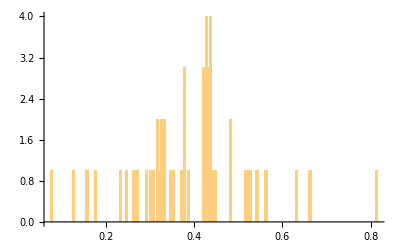

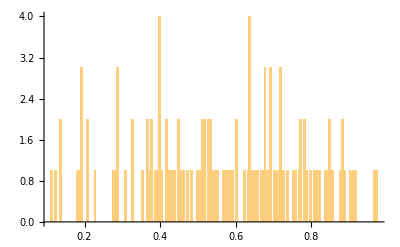

n= 580, Vocab Entropy:0.390731, Doc Entropy:0.395287

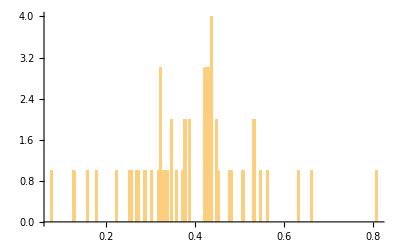

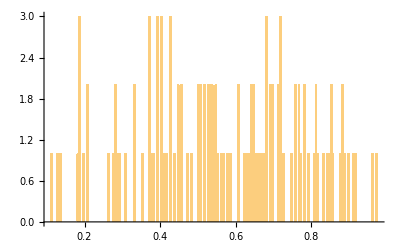

n= 600, Vocab Entropy:0.390052, Doc Entropy:0.367382

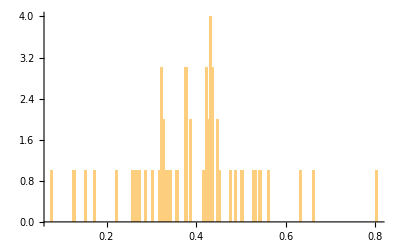

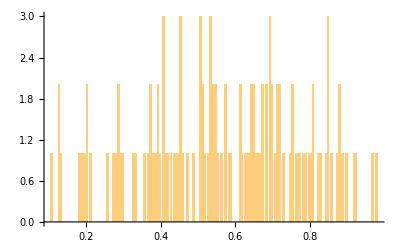

n= 620, Vocab Entropy:0.389827, Doc Entropy:0.393586

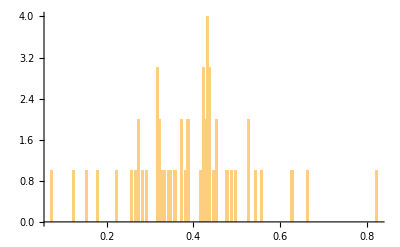

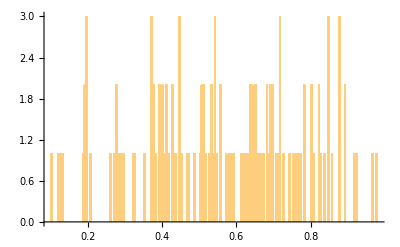

n= 640, Vocab Entropy:0.390008, Doc Entropy:0.384072

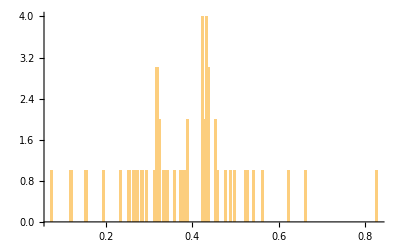

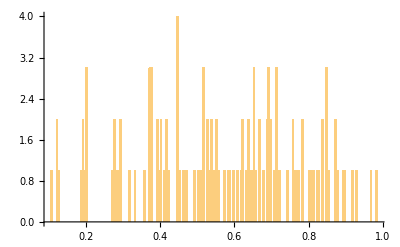

n= 660, Vocab Entropy:0.389684, Doc Entropy:0.379481

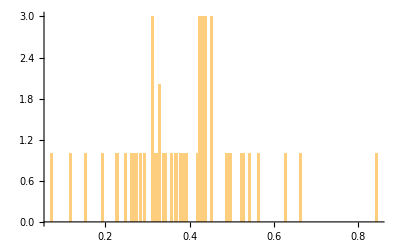

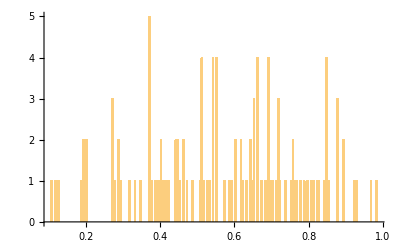

n= 680, Vocab Entropy:0.389764, Doc Entropy:0.403544

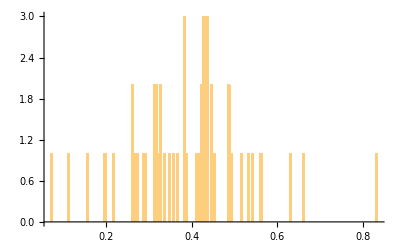

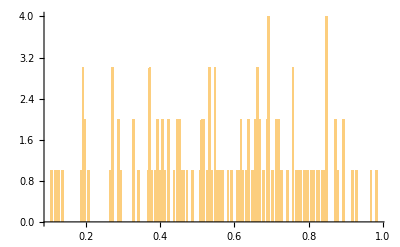

n= 700, Vocab Entropy:0.389681, Doc Entropy:0.381498

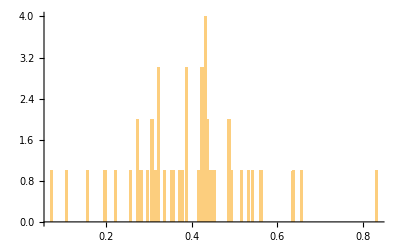

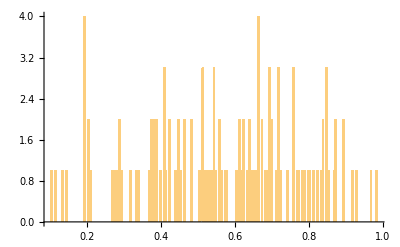

n= 720, Vocab Entropy:0.389962, Doc Entropy:0.366768

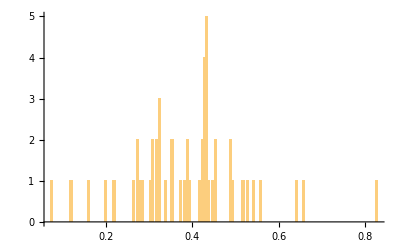

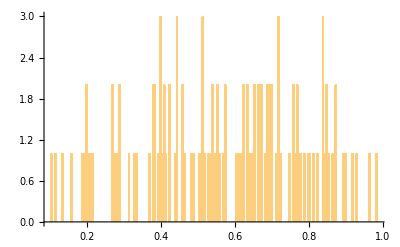

n= 740, Vocab Entropy:0.389553, Doc Entropy:0.399756

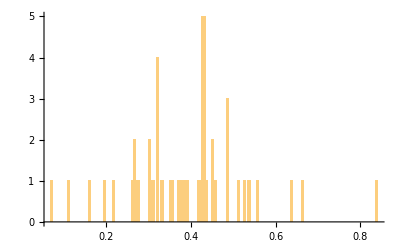

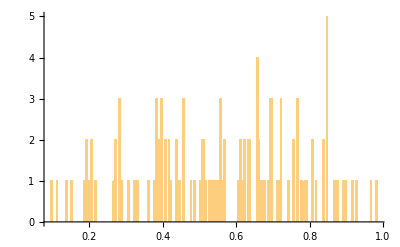

n= 760, Vocab Entropy:0.389032, Doc Entropy:0.372486

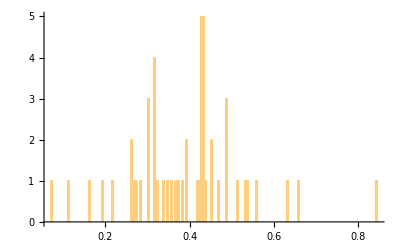

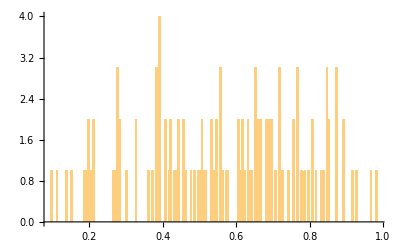

n= 780, Vocab Entropy:0.389597, Doc Entropy:0.371326

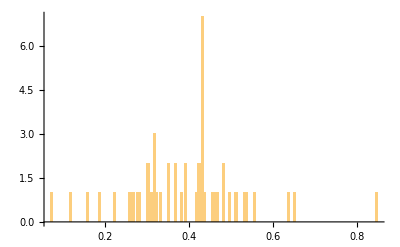

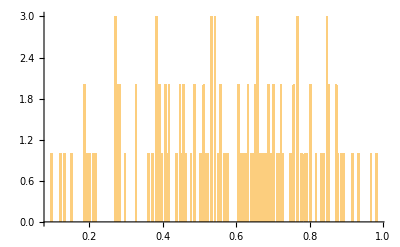

n= 800, Vocab Entropy:0.389641, Doc Entropy:0.369862

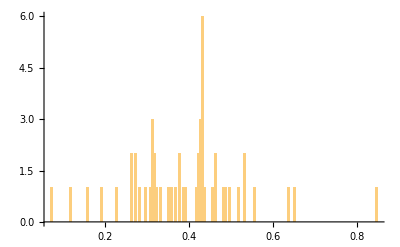

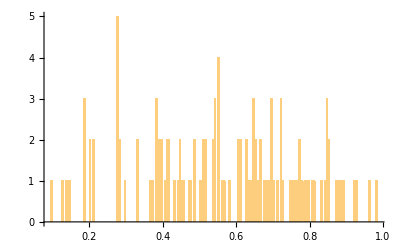

n= 820, Vocab Entropy:0.390449, Doc Entropy:0.387338

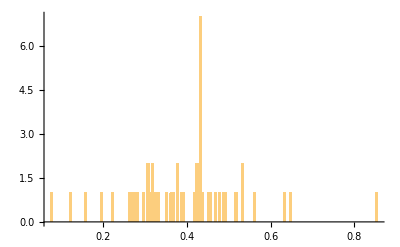

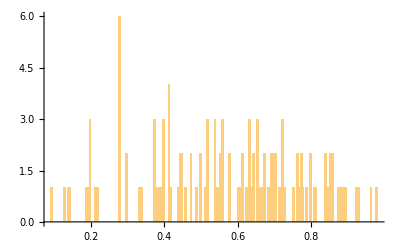

n= 840, Vocab Entropy:0.390043, Doc Entropy:0.38869

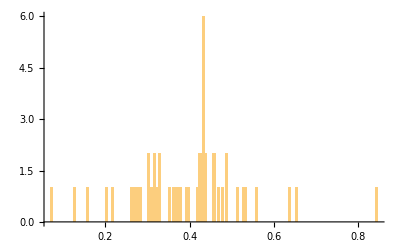

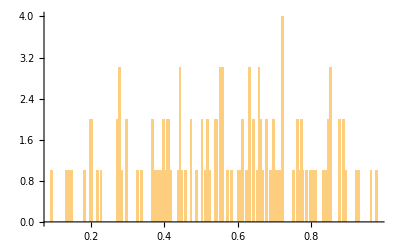

n= 860, Vocab Entropy:0.38917, Doc Entropy:0.389948

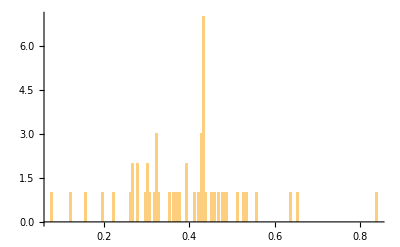

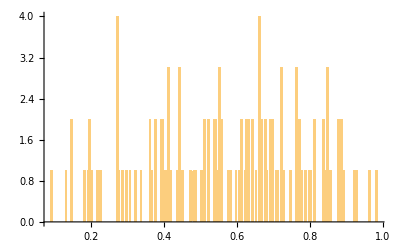

n= 880, Vocab Entropy:0.389073, Doc Entropy:0.392432

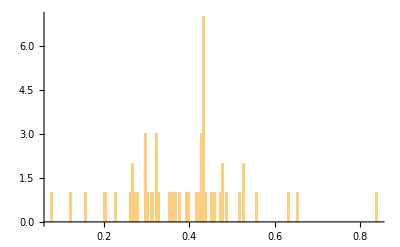

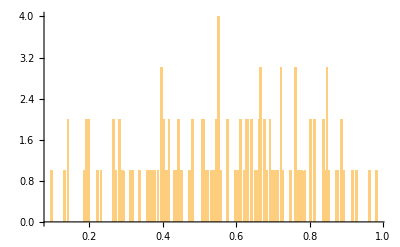

n= 900, Vocab Entropy:0.38962, Doc Entropy:0.380616

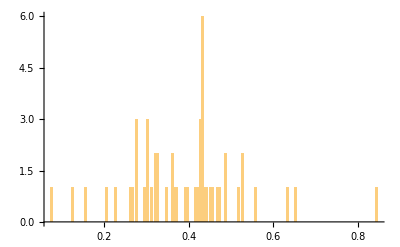

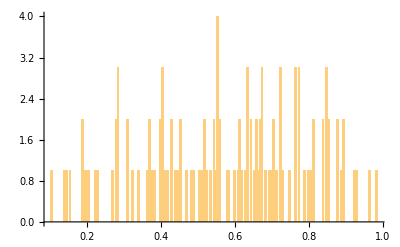

n= 920, Vocab Entropy:0.38953, Doc Entropy:0.371758

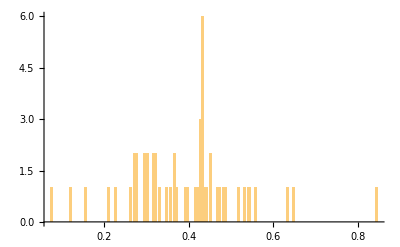

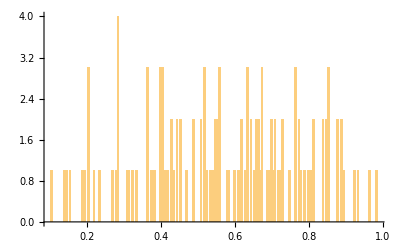

n= 940, Vocab Entropy:0.389427, Doc Entropy:0.37747

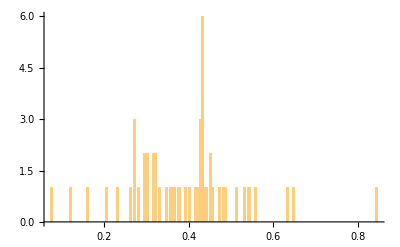

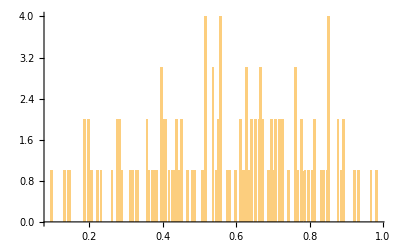

n= 960, Vocab Entropy:0.38978, Doc Entropy:0.383349

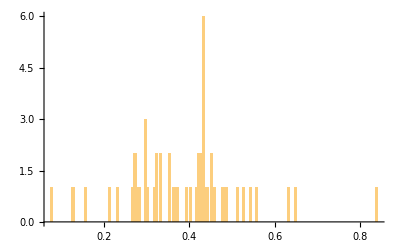

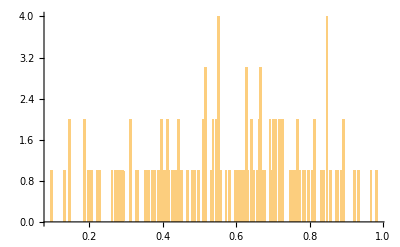

n= 980, Vocab Entropy:0.390001, Doc Entropy:0.366331

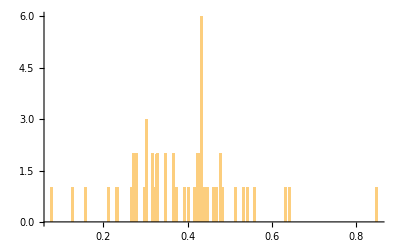

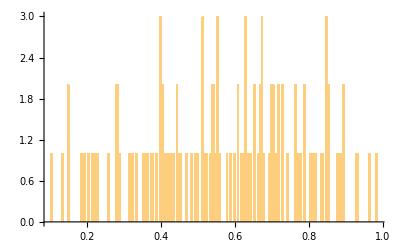

n= 1000, Vocab Entropy:0.390042, Doc Entropy:0.3771

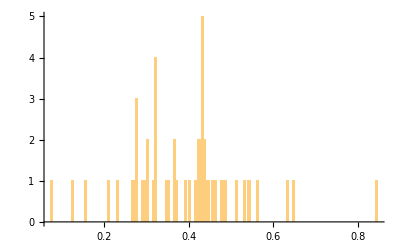

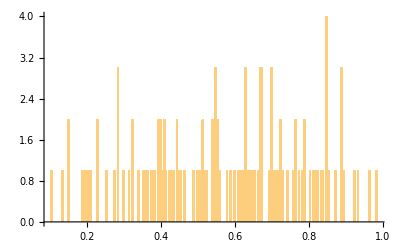

16392.19188

Wed 30 Mar 2022 13:40:30GMT-4[]

Wed 30 Mar 2022 18:13:42GMT-4[]

```mathematica
t1=AbsoluteTime[];
startTime=Now[]
SeedRandompaclet:ref/SeedRandom[];
tm="5";
kk=0;
sumNormLog={};
(*dt1OutputOld=If[reTest>=3,dt1Output,dt1OutputOld];*)
(*vocabTopic5IntOld=If[reTest>=3,vocabTopic5Int,vocabTopic5IntOld];*)
Print["Beginning vocab Entropy: ", N@vocabTopic3EntAccBeg/vmax,", Beginning doc Entropy: ",N@docTopic3EntBeg/dmax];
vocabCntsEnt=Map[{Total[#],entropyF[#]}&,vocabTopic3];
vocabCntsEntP={};
vt1={};
dt1={};
dtClass1=Table[{},{i,1,nmax}];
vtClass1=Table[{},{i,1,nmax}];
dtClass2=Table[{},{i,1,nmax}];
vtClass2=Table[{},{i,1,nmax}];
dtClass3=Table[{},{i,1,nmax}];
vtClass3=Table[{},{i,1,nmax}];
Histogram[#[[2]]&/@vocabCntsEnt]
(***********Iteration begins************)
Do[
If[ran==0,Goto[noran]];
assignsOrd=SortBy[Table[{order1Reo[[i]], assigns[[i]]},{i,1,Length[assigns]}],#[[1]]&];
wmaxOrd=SortBy[Table[{order1Reo[[i]], wmax[[i]]},{i,1,Length[assigns]}],#[[1]]&];
assigns=#[[2]]&/@assignsOrd;
wmax=#[[2]]&/@wmaxOrd;
order2=RandomSample[Range[1,Length[assigns]]];
assignsRan=SortBy[Table[{order1[[i]],order2[[i]], assigns[[i]]},{i,1,Length[assigns]}],#[[2]]&];
docTopic3Ran=SortBy[Table[{order1[[i]],order2[[i]], docTopic3[[i]]},{i,1,Length[assigns]}],#[[2]]&];
wmaxRan=SortBy[Table[{order1[[i]],order2[[i]], wmax[[i]]},{i,1,Length[assigns]}],#[[2]]&];
order1Reo=#[[1]]&/@assignsRan;
assigns=#[[3]]&/@assignsRan;
docTopic3=#[[3]]&/@docTopic3Ran;
wmax=#[[3]]&/@wmaxRan;
Label[noran];
Do[
assignCurDoc=assigns[[d]];(*3 component {word, vocab-index, topic}*)
docTopic3Cur=docTopic3[[d]]; (*current doc topic distribution*)
(*sumV=Total[vocabTopic3];*)
(*total assignment counts by topic, updated once per iteration even though it changes with every assignment change*)
Do[
(*docSum=If[MemberQ[subjWLcnt,dataIX[[d]]],20,5];*)
Do[
ta=AbsoluteTime[];
sumV=Total[vocabTopic3];
kk=kk+1;
assignCur=assignCurDoc[[w]];(*grab assignment to current word, {word,index, topic assignment}*)
(*ERROR CHECKING CODE*)
If[docTopic3Cur[[assignCur[[3]]]]==0,doczeroCnt=doczeroCnt+1];
If[docTopic3Cur[[assignCur[[3]]]]==0,Print["n: ",n," d: ",d," w: ",w, assignCur,docTopic3Cur]];
If[docTopic3Cur[[assignCur[[3]]]]==0,Abort[]];
docTopic3Cur[[assignCur[[3]]]]=If[docTopic3Cur[[assignCur[[3]]]]>0,docTopic3Cur[[assignCur[[3]]]]-1,Print["PROBLEM!"]];
(*docCaseEntBeg=entropyF[docTopic3[[d]]];
vocabCaseEntBeg=entropyF[vocabTopic3[[assignCur[[2]]]]];*)
(*HERE*)
docTopic3[[d,assignCur[[3]]]]=docTopic3[[d,assignCur[[3]]]]-1;(*reduce count by one in doc distribution for topic assignment of current word as long as it is non-zero*) 
(*doc multinomial distribution factor*)
tb=AbsoluteTime[];
tt1=Total[vocabTopic3[[assignCur[[2]]]]];
(*reduce count by one in vocab distribution for topic assignment of current word as long as it is non-zero*) 
vocabTopic3[[assignCur[[2]],assignCur[[3]]]]=If[vocabTopic3[[assignCur[[2]],assignCur[[3]]]]>0,vocabTopic3[[assignCur[[2]],assignCur[[3]]]]-1,Print["PROBLEM!"]];
tc=AbsoluteTime[];
(*distUpd=docTopicDistUpd*vocabTopicDistUpd;*)(*mutiply factors, don't worry about renormalization?*)
(*vRowSum=Total[x];( should be a sum of a row of VT, check for variable*)
(*+(alpha*beta/sumV)*)
(*___________________Burn-in adjustments__________________*)
(*nVoc is iteration at which mixing starts*)
vocabDist1=If[(Total[vocabTopic3[[assignCur[[2]]]]]≤10)&&n<nVoc,ConstantArray[Total[vocabTopic3[[assignCur[[2]]]]]/topicnum,topicnum],vocabTopic3[[assignCur[[2]]]]];
docTopic3Cur1=If[wmax[[d]]≤4&&n<nSubj,ConstantArray[Total[docTopic3Cur]/topicnum,topicnum],docTopic3Cur];
docTopic3Cur2=docTopic3Cur1;
vocabDist2=vocabDist1;
(*_________________Mixing____________________*)
If[ n≤nSumAvg,Goto[skipSumAvg]];
(*If[FractionalPart[n/3*cumFreq]!=0,Goto[skipSumAvg]];*)
docTopic3Cur2=N@mu*docTopic3Cur1+N@((1-mu)*(Total[docTopic3Cur1]/Total[dt1[[d]]])*dt1[[d]]);
vocabDist2=N@nu*vocabDist1+N@((1-nu)*(Total[vocabDist1]/Total[vt1[[assignCur[[2]]]]])*vt1[[assignCur[[2]]]]);
If[n>3000,Abort[]];
Label[skipSumAvg];
(*__________________sumNorm______041621_____________*)
docTopic3CurTot=docTopic3Tot[[d]];
sumV=Total[vocabTopic3];
sumNorm=sumV*(docTopic3CurTot+(topicnum*alpha))+docTopic3CurTot*vmax*beta+topicnum*alpha*vmax*beta;
(*Variations:*)
(*sumNorm1=sumV*(docTopic3CurTot);*)
(*sumNorm2=sumV*topicnum*alpha;*)
(*sumNorm3=docTopic3CurTot*topicnum*alpha;*)
(*sumNorm4=topicnum*alpha*vmax*beta;*)
(*__________________CLASSIFIER___________________*)
distUpd=N[delta*docTopic3Cur2^gammad*vocabDist2^gammav/sumNorm+alpha*vocabDist2/sumNorm+beta*docTopic3Cur2/sumNorm+alpha*beta/sumNorm];
(*distUpd=N[delta*docTopic3Cur2^gammad*vocabDist2^gammav/sumV+alpha*vocabDist2/sumV+beta*docTopic3Cur2/sumV+alpha*beta/sumV];*)
(*Replace topic components beyond top 3 with zeros*)
distUpdN=Take[ReverseSortBy[number[distUpd],#[[2]]&],2];
distUpd=#[[2]]&/@Table[If[Select[distUpdN,#[[1]]==i&]≠{},Select[distUpdN,#[[1]]==i&][[1]],{i,0}],{i,1,topicnum}];
(*for n<nDie, and low count object, make distribution flat*)
topNew=If[(Total[vocabTopic3[[assignCur[[2]]]]]≤10)&&n<nDie,RandomChoice[ConstantArray[1/topicnum,topicnum]->topics],RandomChoice[distUpd->topics]];
assignCur[[3]]=topNew;(*update assignment with new assignment*) 
td=AbsoluteTime[];
assignCurDoc[[w]]=assignCur;(*place assign record in array for doc*)
docTopic3Cur[[topNew]]=docTopic3Cur[[topNew]]+1;
(*Takes incremented docTopic3Cur and inserts into document/topic location for docTopic3*)
docTopic3[[d,topNew]]=docTopic3Cur[[topNew]];
(*Increments vocab topic count*)
vocabTopic3[[assignCur[[2]],topNew]]=vocabTopic3[[assignCur[[2]],topNew]]+1;
tt2=Total[vocabTopic3[[assignCur[[2]]]]];
If[tt2-tt1≠0,Print["d: ",d,",w: ",w,",diff: ", tt2-tt1]];
(*If[tt2-tt1≠0,Pause[3]];*)
te=AbsoluteTime[];
k=k+1;
assigns[[d,w]]=assignCurDoc[[w]];,
{w,1,wmax[[d]]}];,
{w2,1,docSum}];,
{d,dmin,dmax}];
(*****Randomize samples before next iteration*****)
If[ran==0,Goto[noran1]];
docTopic3Ord=SortBy[Table[{order1Reo[[i]], docTopic3[[i]]},{i,1,Length[assigns]}],#[[1]]&];
docTopic3=#[[2]]&/@docTopic3Ord;
Label[noran1];
(**************Assignment Accumulation**************)
dt=docTopic3;
If[n==cumNum,dt1=dt];If[n>cumNum&&FractionalPart[n/cumFreq]==0,dt1=dt+dt1];
(**************Convergence Logging**************)
dtClass1[[n]]=ToExpression[StringSplit[topTopicsF[#],":"][[1]]]&/@dt1;
dtClass2[[n]]=ToExpression[StringSplit[topTopicsF[#],":"][[2]]]&/@dt1;
dtClass3[[n]]=ToExpression[StringSplit[topTopicsF[#],":"][[3]]]&/@dt1;
(**************Assignment Accumulation**************)
vt=vocabTopic3;
If[n==cumNum,vt1=vt];If[n>cumNum&&FractionalPart[n/cumFreq]==0,vt1=vt+vt1];
(****************Convergence Logging*****************)
vtClass1[[n]]=ToExpression[StringSplit[topTopicsF[#],":"][[1]]]&/@vt1;
vtClass2[[n]]=ToExpression[StringSplit[topTopicsF[#],":"][[2]]]&/@vt1;
vtClass3[[n]]=ToExpression[StringSplit[topTopicsF[#],":"][[3]]]&/@vt1;
tn=topNew;
tf=AbsoluteTime[];
(************Progress Histograms****************)
vocabTopic3EntEnd=Total[Map[entropyF[#]&,vt1]];
docTopic3EntEnd=Total[Map[entropyF[#]&,docTopic3]];
If[FractionalPart[n/frq]!=0,Goto[continue]];
If[FractionalPart[n/frq]==0,Print["n= ",n, ", Vocab Entropy:", N@vocabTopic3EntEnd/vmax,", Doc Entropy:",N@ docTopic3EntEnd/dmax]];
vocabCntsEnt=If[FractionalPart[n/frq]==0,Map[{Total[#],entropyF[#]}&,vocabTopic3],vocabCntsEnt];
vocabCntsEntP=If[FractionalPart[n/frq]==0,Map[{Total[#],entropyF[#]}&,vt1],vocabCntsEntP];
If[FractionalPart[n/frq]==0,Print[Histogram[#[[2]]&/@vocabCntsEntP,{0.005}]]];
If[FractionalPart[n/frq]==0,Print[Histogram[Map[entropyF[#]&,dt1],{0.005}]]];
Label[continue];
If[ n==nmax, Goto[final]];
Label[final];
If[nmax≤500,Print["n: ",n]];,
{n,1,nmax}];
(*------------------End of Iterations--------------------------*)
finalEntropies="n= "<>ToString[nmax]<> ", Vocab Entropy:"<>ToString[ N@vocabTopic3EntEnd/vmax]<>", Doc Entropy:"<>ToString[N@ docTopic3EntEnd/dmax];
(*-----------------------Output Preparation---------------------*)
dtN=Map[norm[#]&,dt];
vocabTopic4=Map[{vocab[[#]],vocabTopic3[[#]]}&,Range[1,vmax]];
vocabTopic5=Flatten[#]&/@vocabTopic4;
vtst1=Map[{Total[#[[2]]],entropyF[#[[2]]]}&,vocabTopic4];
vocabTopic5Ent=Map[{vocab[[#]],vtst1[[#]]}&,Range[1,vmax]];
(*vocabTopic5Ent=Map[{vocab[[#]],Map[{Total[#[[2]]],entropyF[#[[2]]]}&,vocabTopic4][[#]]}&,Range[1,vmax]];*)
vocabTopic4Int=Map[{vocab[[#]],vt1[[#]]}&,Range[1,vmax]];
vocabTopic5Int=Flatten[#]&/@vocabTopic4Int;
vtst2=Map[{Total[#[[2]]],entropyF[#[[2]]]}&,vocabTopic4Int];
vocabTopic5IntEnt=Map[{vocab[[#]],vtst2[[#]]}&,Range[1,vmax]];
dtOutputCnts=MapIndexed[Flatten@{#2[[1]],topTopicsF[#],#}&,dt];
dtOutput=MapIndexed[Flatten@{#2[[1]],topTopicsF[#],#}&,dtN];
dt1N=Map[norm[#]&,dt1];
dt1Output=MapIndexed[Flatten@{#2[[1]],topTopicsF[#],#}&,dt1N];
dt1OutputCnts=MapIndexed[Flatten@{#2[[1]],topTopicsF[#],#}&,dt1];
vocabCnt1Ent=Table[Flatten[{vocabCnt1[[i]],entropyF[vocabTopic4Int[[i,2]]]}],{i,1,Length[vocabCnt1]}];
(*-------------------Class Mapping Attempt-------------------------*)
(*Attempts to map classes based on total samples within class*)
(*Assumes that parameters have achieved repeatability and number of samples in class is stable*)
(*from run to run*)
mapper=MapIndexed[{#1,#2[[1]]}&,(#[[1]]&/@Reverse@SortBy[Tally[ToExpression[StringSplit[#[[2]],":"][[1]]]&/@dt1Output],Last])];
mapperOrd=#[[1]]&/@mapper;
Do[ixToNewIX[mapper[[i,1]]]=mapper[[i,2]],{i,1,topicnum}];
assignsTr=Map[{#[[1]],#[[2]],ixToNewIX[#[[3]]]}&,assigns,{2}];
assigns=assignsTr;
dtOutputCntsTr=Map[Flatten@{#[[1]],StringRiffle[ixToNewIX[#]&/@ToExpression[StringSplit[#[[2]],":"]],":"],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-1]]}&,dtOutputCnts];
dtOutputCnts=dtOutputCntsTr;
dtOutputTr=Map[Flatten@{#[[1]],StringRiffle[ixToNewIX[#]&/@ToExpression[StringSplit[#[[2]],":"]],":"],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-1]]}&,dtOutput];
dtOutput=dtOutputTr;
vocabTopic5Tr=Map[Flatten@{#[[1]],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-2]]}&,vocabTopic5];
vocabTopic5=vocabTopic5Tr;
vocabTopic5IntTr=Map[Flatten@{#[[1]],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-2]]}&,vocabTopic5Int];
vocabTopic5Int=vocabTopic5IntTr;
vocabTopic5Int1=Flatten@{#[[1]],topTopicsF[#[[2;;]]]}&/@vocabTopic5Int;
dt1OutputCntsTr=Map[Flatten@{#[[1]],StringRiffle[ixToNewIX[#]&/@ToExpression[StringSplit[#[[2]],":"]],":"],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-1]]}&,dt1OutputCnts];
dt1OutputCnts=dt1OutputCntsTr;
dt1OutputTr=Map[Flatten@{#[[1]],StringRiffle[ixToNewIX[#]&/@ToExpression[StringSplit[#[[2]],":"]],":"],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-1]]}&,dt1Output];
dt1Output=dt1OutputTr;
(*-----------Future for Automated reurn comparisons-----------*)
(*dt1OutputOld=Which[reTest==1,dt1Output,reTest==2,dt1OutputOld,reTest≥3,dt1OutputOld];*)
(*vocabTopic5Int1Old =Which[reTest==1,vocabTopic5Int1,reTest==2,vocabTopic5Int1Old,*)(*reTest≥3,vocabTopic5Int1Old];*)
(*classMem=ConstantArray[1,topicnum];*)
(*classMemOld=ConstantArray[1,topicnum];*)
(*If[reTest==1, Print["Class comparison net valid yet."]];*)
(*classMem=Map[#[[1]]&,Map[#[[2]]&,Reverse@SortBy[Normal[GroupBy[{#[[1]],StringSplit[#[[2]],":"][[1]]}&/@dt1Output,Last]],Length[#[[2]]]&],{1}],{2}];*)
(*classMemOld=Map[#[[1]]&,Map[#[[2]]&,Reverse@SortBy[Normal[GroupBy[{#[[1]],StringSplit[#[[2]],":"][[1]]}&/@dt1OutputOld,Last]],Length[#[[2]]]&],{1}],{2}];*)
(*classComp=N@Length@Intersection[classMemOld[[#]],classMem[[#]]]/Length[classMemOld[[#]]]&/@Range[topicnum]*)
(*----------Future Under development, rerun cont.-------------*)
(*vocabClassMem=Map[#[[1]]&,Map[#[[2]]&,Reverse@SortBy[Normal[GroupBy[{#[[1]],StringSplit[#[[2]],":"][[1]]}&/@vocabTopic5Int1,Last]],Length[#[[2]]]&],{1}],{2}];
vocabClassMemOld=Map[#[[1]]&,Map[#[[2]]&,Reverse@SortBy[Normal[GroupBy[{#[[1]],StringSplit[#[[2]],":"][[1]]}&/@vocabTopic5Int1Old,Last]],Length[#[[2]]]&],{1}],{2}];
vocabClassComp=N@Length@Intersection[vocabClassMemOld[[#]],vocabClassMem[[#]]]/Length[vocabClassMemOld[[#]]]&/@Range[topicnum]
reTest=If[reset==0,reTest+1,reTest];*)
(*----------Refresh of Readme file with some new info from run-------------*)
tg=AbsoluteTime[];
readme=name<>nameExt<>"\n"<>"TopicNum: "<>ToString[topicnum]<>"\n"<>
"Run #: "<>ToString[runVal]<>"\n"<>
"Input filename: "<>inputFilename<>"\n"<>
"Word Column Num: "<>ToString[wordColnum]<>"\n"<>
"Word Cutoff: "<>ToString[wordCutoff]<>"\n"<>
"alpha: "<>ToString[alpha]<>"\n"<>
"beta: "<>ToString[beta]<>"\n"<>
"gammad: "<>ToString[gammad]<>"\n"<>
"gammav: "<>ToString[gammav]<>"\n"<>
"delta: "<>ToString[delta]<>"\n"<>
"TM: "<>tm<>"\n"<>
"Option: "<>ToString[option]<>"\n"<>
"# of entities: "<>ToString[Length@datatest1]<>"\n"<>
"Cumulative starting point: "<>ToString[cumNum]<>", Cumulative Frequency: "<>ToString[cumFreq]<>"\n"<>
"Ending Vocab Entropy: "<>ToString[ N@vocabTopic3EntEnd/vmax]<>" Ending Doc Entropy: "<>ToString[N@ docTopic3EntEnd/dmax]<>"\n"<>
"# of Iterations: "<>ToString[nmax]<>"\n"<>note;
t2=AbsoluteTime[];
(*Topics end*)
Print[t2-t1]
startTime
stopTime=Now[]
```

### Mapping for Summation

>>>Mapping
>>> Intended to be used in manual process of adding reruns becauses classes may not be the same from run to run.
>>> Detailed documentation of manual process is not available yet.
>>> Get in touch with the author through github or corresonding author of paper

```mathematica
dt1OutputCnts=Import["Alzheimers_AK_only_6_topics_a_0P3_b_0P25_cut_1_12.11_docTopicCntsInt3.csv"];
```

```mathematica
dt1Output=Table[Flatten@{i,topTopicsF[dt1OutputCnts[[i,3;;]]],norm[dt1OutputCnts[[i,3;;]]]},{i,1,Length@dt1OutputCnts}];
Length@dt1Output
```

```mathematica
mapperInput={1,2,3,5,4};
mapper={mapperInput[[#]],#}&/@Range[topicnum]
```

{{1,1},{2,2},{3,3},{5,4},{4,5}}

```mathematica
mapperOrd=#[[1]]&/@mapper;
Do[ixToNewIX[mapper[[i,1]]]=mapper[[i,2]],{i,1,topicnum}];
```

```mathematica
dt1OutputCntsTr=Map[Flatten@{#[[1]],StringRiffle[ixToNewIX[#]&/@ToExpression[StringSplit[#[[2]],":"]],":"],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-1]]}&,dt1OutputCnts];
dt1OutputTr=Map[Flatten@{#[[1]],StringRiffle[ixToNewIX[#]&/@ToExpression[StringSplit[#[[2]],":"]],":"],#[[((mapperOrd[[#]])&/@Range[topicnum])+datacol-1]]}&,dt1Output];
```

```mathematica
dt1Output=dt1OutputTr;
dt1OutputCnts1=dt1OutputCntsTr;
dt1OutputCnts=dt1OutputCntsTr;
```

```mathematica
datacol
```

3

>>> Export Rerun

```mathematica
dt1OutputCnts[[2]]
```

{2,1:2:3,224,120,10,1,9}

```mathematica
dt1Output[[2]]
```

{2,1:2:5,0.67033,0.272527,0.0186813,0.0032967,0.0351648}

```mathematica
Export[prefix<>"_docTopicCntsIntSum.csv",dt1OutputCnts,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.14_docTopicCntsInt1.csv

```mathematica
dt1OutputCnts=Import["Alzheimers_AK_only_6_topics_a_0P3_b_0P25_cut_1_12.11_docTopicCntsInt3.csv"];
```

```mathematica
Export[prefix<>"_docTopicCntsIntSum_redo.csv",dt1OutputCnts,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.14_docTopicCntsIntSum_redo.csv

```mathematica
Export[prefix<>"_docTopicSum.csv",dt1Output,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.14_docTopicSum.csv

>>>Tally
working on 1
  done

>>> for Sum

```mathematica
dt1Output=Table[Flatten@{i,topTopicsF[dt1OutputCntsSum[[i]]],norm[dt1OutputCntsSum[[i]]]},{i,1,Length@dt1OutputCntsSum}];
```

```mathematica
dt1Output[[152]]
```

{152,5:6:4,0.023871,0.036129,0.0509677,0.226774,0.349032,0.313226}

```mathematica
dt1OutputCnts4[[33]]
```

{33,2:4:1,27,135,17,46,14,9}

>>> After import but not remap

```mathematica
dt1OutputCnts=dt1OutputCnts3;
```

```mathematica
dt1Output=Table[Flatten@{i,topTopicsF[dt1OutputCnts[[i,3;;]]],norm[dt1OutputCnts[[i,3;;]]]},{i,1,Length@dt1OutputCnts}];
```

```mathematica
dt1OutputCnts5[[16]]
dt1Output[[16]]
```

dt1OutputCnts5⟦16⟧

{16,3:1:2,0.227273,0.2,0.572727}

```mathematica
{Length@dt1OutputCnts1,Length@dt1OutputCnts2,Length@dt1OutputCnts3,Length@dt1OutputCnts4,Length@dt1OutputCnts5}
```

{122,122,122,122,0}

```mathematica
dt1OutputCnts1[[122]]
```

{122,5:1:2,81,26,10,16,177}

>>>> 1 + 2 + 3 +4 +5

```mathematica
dt1OutputCntsSum=Table[dt1OutputCnts1[[i,3;;]]+dt1OutputCnts2[[i,3;;]]+dt1OutputCnts3[[i,3;;]]+dt1OutputCnts4[[i,3;;]]+dt1OutputCnts5[[i,3;;]],{i,1,Length@dt1OutputCnts1}];
```

```mathematica
dt1OutputCnts1[[1,3;;]]
```

{78,161,2,0,123}

```mathematica
dt1OutputCntsSum=Table[dt1OutputCnts1[[i,3;;]]+dt1OutputCnts2[[i,3;;]]+dt1OutputCnts4[[i,3;;]]+dt1OutputCnts5[[i,3;;]],{i,1,Length@dt1OutputCnts1}];
```

```mathematica
dt1OutputCntsSum[[30]]
```

{421,406,634,146,332,231}

```mathematica
dt1OutputCntsSum=Table[dt1OutputCnts1[[i,3;;]]+dt1OutputCnts4[[i,3;;]]+dt1OutputCnts5[[i,3;;]],{i,1,Length@dt1OutputCnts1}];
```

```mathematica
dt1OutputSum=Table[Flatten@{i,topTopicsF[dt1OutputCntsSum[[i]]],norm[dt1OutputCntsSum[[i,1;;]]]},{i,1,Length@dt1OutputCntsSum}];
```

```mathematica
dt1Output=dt1OutputSum;
```

```mathematica
dt1Output[[3]]
```

{3,1:2:5,0.489247,0.266129,0.0322581,0.0268817,0.185484}

```mathematica
O
```

```mathematica
s=113;
dt1OutputCnts1[[s]]
dt1OutputSum[[s]]
```

{113,3:1:5,89,73,92,41,77}

{113,1:5:3,{0.250538,0.167742,0.186559,0.169355,0.225806}}

```mathematica
dt1OutputCnts1[[33]]
```

{33,2:1:4,86,122,5,20,15}

```mathematica
dt1Output=Table[Flatten@{i,topTopicsF[dt1OutputCnts2[[i,3;;]]],norm[dt1OutputCnts2[[i,3;;]]]},{i,1,Length@dt1OutputCnts2}];
```

```mathematica
dt1Output[[55]]
```

{55,1:5:3,0.396774,0.158065,0.158065,0.083871,0.203226}

```mathematica
datacol
```

## Export

>>> Using the parameters of the XXX, filenames are created for key variable export to the current directory. 
>>> prefix
>>> assigns: final assignment by sample for each object. Note this is the last assignment and not much use.
>>> dtOutputCnts: sample class count distributions after last iteration
>>> dtOutput: normalized class distributions after last iteration
>>> vocabTopic5: object class count distributions after last iteration
>>> vocabTopic5Int: accumulated object class count distribution for thinned iterations
>>> dt1OutputCnts: accumulated sample class count distributions for thinned iterations
>>> dt1Output: accumulated normalized sample class count distributions for thinned iterations
>>> dataIX: indices of remaining samples after various applied filters 
>>> readme: user description of current run plus automated logging of parameters

```mathematica
readme
```

Alzheimers_AK_only_
TopicNum: 5
Run #: 12.9
Input filename: microbiome_alzheimer's_input_8_s1.tsv
Word Column Num: 2
Word Cutoff: 1
Subject Length Cutoff: 1
alpha: 0.3
beta: 0.25
gamma: 1.
delta: 1.
option: 8
TM: 5
# of entities: 122
Cumulative starting point: 49, Cumulative Frequency: 5
# of Iterations: 350
alzheimer's, Arkansas only, negative controls removed, edited to remove samples with no metadata, no contamination gative controls removed, edited to remove samples with no metadata, no contamination removal, 5 topics, Genus, Option 8,P&A, 12 and above, keep, 11 and below, lo; 14's labeled nonspec-14, collapsers labeled hi (GTE11) or lo(LTE 10), MCntGTE5 and GTE 11, hi, others wise discard, 2nd pass, objCnts LTE 4, mapped to loCnt. very nice graph definition

```mathematica
prefix
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1

```mathematica
Export[prefix<>"_assignsTst.tsv",assigns,"TSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_assignsTst.tsv

```mathematica
Export[prefix<>"_docTopicCnts.csv",dtOutputCnts,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_docTopicCnts.csv

```mathematica
Export[prefix<>"_docTopicFr.csv",dtOutput,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_docTopicFr.csv

```mathematica
Length@dtOutput
```

122

```mathematica
Export[prefix<>"_vocabTopicCnts.csv",vocabTopic5,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_vocabTopicCnts.csv

```mathematica
Export[prefix<>"_vocabTopicCntsInt.csv",vocabTopic5Int,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_vocabTopicCntsInt.csv

```mathematica
Export[prefix<>"_docTopicCntsInt.csv",dt1OutputCnts,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_docTopicCntsInt.csv

```mathematica
Export[prefix<>"_docTopicFrInt.csv",dt1Output,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_docTopicFrInt.csv

```mathematica
Export[prefix<>"_dataIX.csv",dataIX,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_dataIX.csv

```mathematica
Export[prefix<>"_read_me.csv",readme,"CSV"]
```

Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.16rrtst1_read_me.csv

>>>

```mathematica
dt1OutputCnts=Import["Alzheimers_AK_only_5_topics_a_0P3_b_0P25_cut_1_12.9_docTopicCntsInt1.csv"];
```

```mathematica
Export[prefix<>"_docTopicCntsIntSum.csv",dt1OutputCntsSum,"CSV"]
```

Alzheimers_AK_only_5_topics_a_0P3_b_0P25_cut_1_12.9_docTopicCntsIntSum.csv

```mathematica
prefix
```

Alzheimers_AK_only_5_topics_a_0P3_b_0P25_cut_1_12.9

## Analysis

### Convergence Monitoring - Class Assignment Stability

>>> In the classification code several variables are used to capture convergence
>>> They are dtClass1, 2 and 3 and vtClass1, 2 and3.
>>> The dtClass monitor sample convergence and the vtClass monitor object convergence
>>> After each complete iteration through the samples, the top three classes assigned for each sample and object are logged.
>>> The most prevalent class is shown in blue, the second most in orange and the third in green
>>> The graphs show the class assigned on the vertical axis and the x axis shows the iteration counted from burn-in

```mathematica
st=150;stop=1000;
Table[ListLinePlot[{ixToNewIX[#]&/@(Transpose[Table[dtClass1[[i]],{i,st,Length@dtClass1}]][[s]]),ixToNewIX[#]&/@(Transpose[Table[dtClass2[[i]],{i,st,Length@dtClass1}]][[s]]),ixToNewIX[#]&/@(Transpose[Table[dtClass3[[i]],{i,st,Length@dtClass1}]][[s]])},PlotLabel->ToString[dataIX[[s]]]<>". "<>ToString[Length[datatest1[[s]]]],PlotRange->{{0,stop},{0,topicnum}}],{s,1,122}]
```

```mathematica
Table[ListLinePlot[ixToNewIX[#]&/@(Transpose[Table[dtClass1[[i]],{i,st,Length@dtClass1}]][[s]]),PlotLabel->ToString[dataIX[[s]]]<>". "<>ToString[Length[datatest1[[s]]]],PlotRange->{{0,stop},{0,6}}],{s,1,122}]
```

```mathematica
Table[ListLinePlot[{ixToNewIX[#]&/@(Transpose[Table[vtClass1[[i]],{i,st,Length@vtClass1}]][[v]]),ixToNewIX[#]&/@(Transpose[Table[vtClass2[[i]],{i,st,Length@vtClass2}]][[v]]),ixToNewIX[#]&/@(Transpose[Table[vtClass3[[i]],{i,st,Length@vtClass3}]][[v]])},PlotRange->{{0,stop},{0,6}},PlotLabel->ToString[v]<>": "<>vocabCnt1[[v,1]]<>", "<>ToString[vocabCnt1[[v,2]]]],{v,1,52}]
```

### Entropy vs. Counts for Microbial Object - Tooltip active for each point

>>> after computing the below, mouse over the points to see the name of the object, its entropy and total counts assigned

```mathematica
vocabCntsEnt1=Map[Tooltip[{Total[#[[2]]],entropyF[#[[2]]]},{#[[1]],entropyF[#[[2]]],Total[#[[2]]]}]&,vocabTopic4Int];
```

```mathematica
vocabCntsEntComp=Map[Flatten@{#[[1]],topTopicsF[#[[2]]],Total[#[[2]]],entropyF[#[[2]]],norm[#[[2]]]}&,vocabTopic4Int];
```

```mathematica
vocabCntsEnt2=Map[Tooltip[{Total[#[[2]]],entropyF[#[[2]]]},{#[[1]],entropyF[#[[2]]],Total[#[[2]]]}]&,vocabTopic4];
```

```mathematica
vocabCntsEntComp2=Map[Flatten@{#[[1]],topTopicsF[#[[2]]],Total[#[[2]]],entropyF[#[[2]]],norm[#[[2]]]}&,vocabTopic4];
```

```mathematica
CntsEntPlot=ListPlot[vocabCntsEnt1,AxesLabel->{Style["Counts",Orange,Bold,12],Style["Entropy",Orange,Bold,12]},PlotRange->{{0,15000},{0.0,1}}]
```